```mathematica
xstresslist1 = {1508.68, 2349.67, 3698.19, 2681.5,  3038.53, 4276.36, 3988.33, 13995.6};
ystresslist1 = {178.059, 4150.98, 3957.13, 1588.78, 3604.45, 144.571, 1243.41, 11261.4};
cellNumber = {10,20,30,40,50,60,70, 80};
data3 = Table[{cellNumber[[i]],xstresslist1[[i]]},{i,8}]
```

{{10,1508.68},{20,2349.67},{30,3698.19},{40,2681.5},{50,3038.53},{60,4276.36},{70,3988.33},{80,13995.6}}

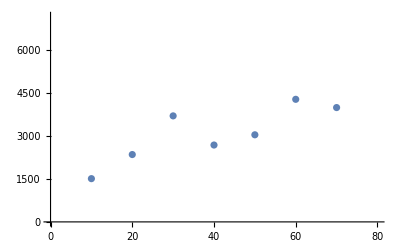

```mathematica
ListPlot[{data3}]
```

```mathematica
line = Fit[data, {1,x}, x]
```

-5331.77+468.219 x

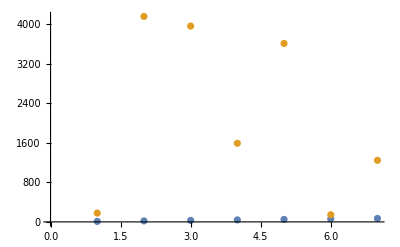

```mathematica
ListPlot[{cellNumber, ystresslist1}]
```

```mathematica
xstresslist2= {-307.303, -4459.11, -1585.15, -3915.41, -2095.63, -1775.68, -1244.81, 5036.07};
xedgeNumber = {5, 7, 7,9 , 10, 9 , 11, 11};
```

```mathematica
data = Table[{xedgeNumber[[i]],xstresslist2[[i]]},{i,8}]
```

{{5,-307.303},{7,-4459.11},{7,-1585.15},{9,-3915.41},{10,-2095.63},{9,-1775.68},{11,-1244.81},{11,5036.07}}

```mathematica
data2 = {{5,307.303},{7,4459.11},{7,1585.15},{9,3915.41},{10,2095.63},{9,1775.68},{11,1244.81},{11,5036.07}}
```

{{5,307.303},{7,4459.11},{7,1585.15},{9,3915.41},{10,2095.63},{9,1775.68},{11,1244.81},{11,5036.07}}

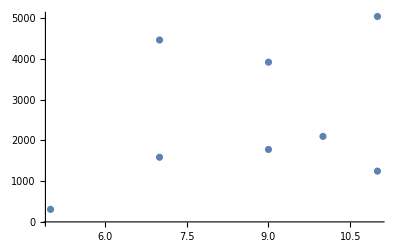

```mathematica
ListPlot[data2]
```

```mathematica
agxstress ={0.108657, 0.309021, 0.646318, 0.428747, 0.205412}; 
agystress = {0.0522188, 0.213593, 0.493692, 0.681417, 0.44359};
cellNum = {10,30,50,70,100};
```

```mathematica
agdatax = Table[{cellNum[[i]],agxstress[[i]]},{i,5}];
agdatay = Table[{cellNum[[i]],agystress[[i]]},{i,5}];
```

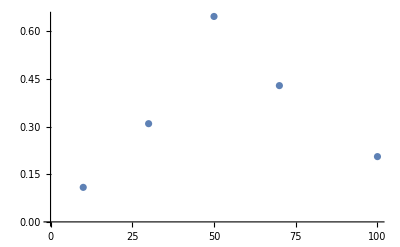

```mathematica
ListPlot[agdatax]
```

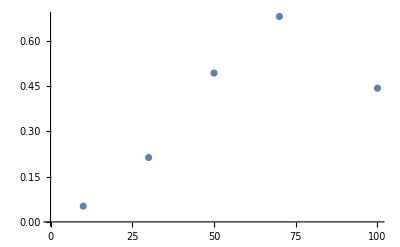

```mathematica
ListPlot[agdatay]
```

```mathematica
cxstress = {0.363385,0.491443, 0.805936, 0.722582, 0.410656};
cystress = {0.165012, 0.504381, 0.695849, 0.638946, 0.529327};
cdatax = Table[{cellNum[[i]], cxstress[[i]]},{i,5}];
cdatay = Table[{cellNum[[i]], cystress[[i]]},{i,5}];
```

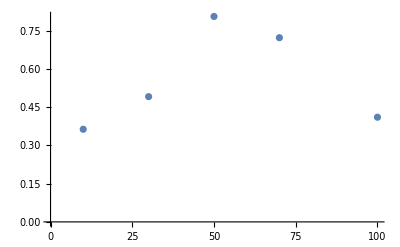

```mathematica
ListPlot[cdatax]
```

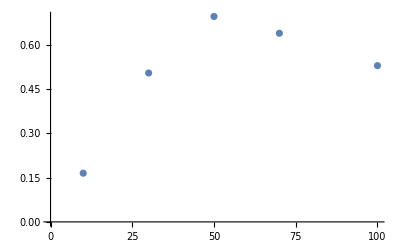

```mathematica
ListPlot[cdatay]
```